```mathematica
Solve[{2 * T * h/Sqrt[h^2 + (0.5*c)^2] == ml * 2 * Sqrt[h^2+ (0.5*c)^2]* g}, T]
```

{{T→(1. g (0.25 c^2+h^2) ml)/h}}

```mathematica
Solve[{T * h1/Sqrt[h1^2 + (0.5*c)^2] + T * h2/Sqrt[h2^2+ (0.5*c)^2] == m&& T * 0.5 *c/Sqrt[h1^2 + (0.5*c)^2] + T * 0.5*c/Sqrt[h2^2+ (0.5*c)^2] == 0} , {T}]
```

{}

```mathematica
GetChord[r_, d_]:= 2*r*Sin[d/(2*r)];
TensionCable[ml_, g_,r_,d_, h_ ]:= (1* g (0.25* GetChord[r, d]^2+h^2) ml)/h;
```

```mathematica
GetDroop[ρ_, g_, r_, d_,T_]:=h /.Solve[{TensionCable[ρ, g, r, d, h] == T}, h][[1]]
```

```mathematica
GetChord[2500, 5000*Pi/2]
```

5000

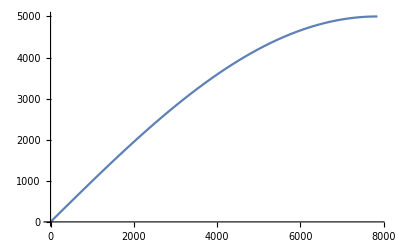

```mathematica
Plot[GetChord[2500,x], {x, 0, Pi * 2500}]
```

```mathematica
TensionCable[0.013, 1.62,10000, 5, 2]
```

0.107932

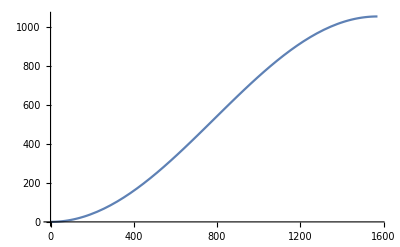

```mathematica
Plot[TensionCable[0.013, 1.62,1000/2, x, 5], {x, 0, Pi * 1000 / 2}]
```

```mathematica
GetDroop[0.013, 1.62,1000/2, x, 2000]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.237417 (200000.-1.41421 √(1.99989×10^10+1.10881×10^6 Cos[0.002 x]))

```mathematica
Subscript[h, rover] = 5;
Subscript[T, cable] = 1500;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

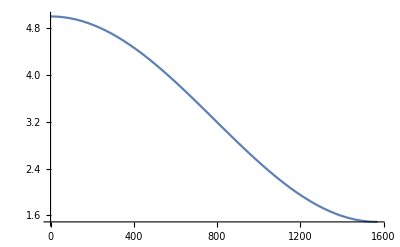

```mathematica
Plot[Subscript[h, rover] - GetDroop[0.013, 1.62,1000/2, x, Subscript[T, cable] ], {x, 0, Pi * 1000 / 2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

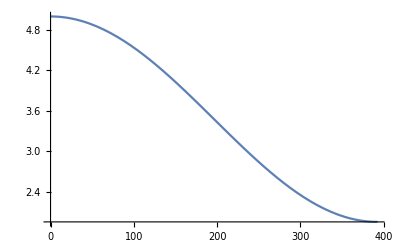

```mathematica
Plot[5 - GetDroop[0.000992109296, 9.81,250/2, x, 50], {x, 0, Pi * 250 / 2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

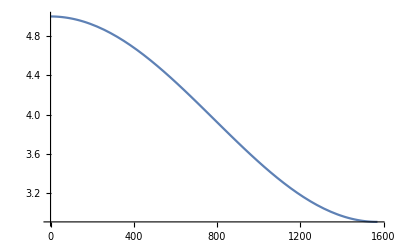

```mathematica
Plot[Subscript[h, rover] - GetDroop[0.000310034155, 1.62,1000/2, x, 60 ], {x, 0, Pi * 1000 / 2}]
```

```mathematica
GetDroopCatenary[λ_,g_,r_, d_, T_]:=(λ*g)* GetChord[r, d]^2/(8 * T);
```

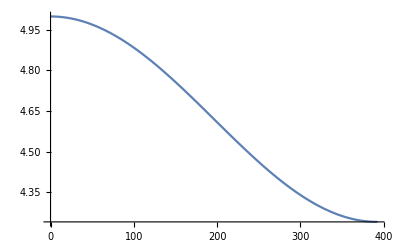

```mathematica
Plot[5- GetDroopCatenary[0.000992109296, 9.81,250/2, x, 100], {x, 0, Pi * 250 / 2}]
```

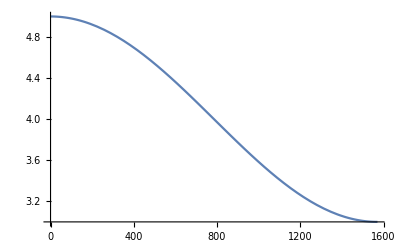

```mathematica
Plot[5- GetDroopCatenary[0.000992109296, 1.62,1000/2, x, 100], {x, 0, Pi * 1000 / 2}]
```